```mathematica
dat=ReadList["V0=0.3.dat"];
datSolitons=Import["BS.txt","Table"];
```

```mathematica
w=dat[[All,1]];
V0=dat[[All,2]];
Mass=dat[[All,3]];
MH=dat[[All,4]];
JH=dat[[All,5]];
Mint=dat[[All,6]];
MintM=dat[[All,7]];
Mints=dat[[All,8]];
Jint=dat[[All,9]];
JintM=dat[[All,10]];
Jints=dat[[All,11]];
TH=dat[[All,12]];
AH=dat[[All,13]];
QeINF=dat[[All,14]];
muINF=dat[[All,15]];
rh=dat[[All,16]];
g=dat[[All,17]];
```

```mathematica
wSolitons = datSolitons[[All,1]];
MSolitons = datSolitons[[All,2]];
JSolitons = datSolitons[[All,3]];
```

```mathematica
len=Length[dat];
lenSolitons=Length[datSolitons];
solitonwM=ListPlot[Table[{wSolitons[[i]],MSolitons[[i]]},{i,1,lenSolitons}],PlotStyle->  Red];
```

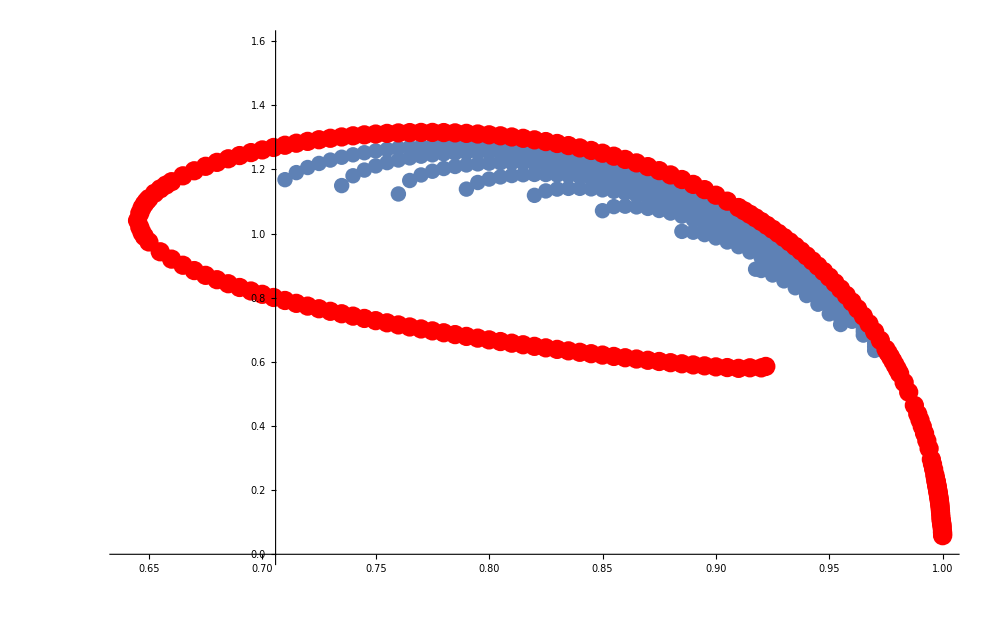

```mathematica
m=ListPlot[Table[{w[[i]],Mass[[i]]},{i,1,len}]];
Show[m,solitonwM,PlotRange->{{0.64,1},{0.,1.6}}]
```

```mathematica
p1=ListPlot[Table[{w[[i]],MH[[i]]},{i,1,len}]];
p2=ListPlot[Table[{w[[i]],Mint[[i]]},{i,1,len}],PlotStyle->Green];
p3=ListPlot[Table[{w[[i]],Mass[[i]]},{i,1,len}],PlotStyle->Red];
Show[p1,p2,p3,PlotRange->{{0.73,1},{0,1.6}}]
```

-Graphics-